## Chapter 7 Figures Figure 7.1

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb,amsfonts}","\\usepackage{lmodern}"}];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dadhikar\Dropbox\Apps\Overleaf\Real_Analysis\chap07\figures

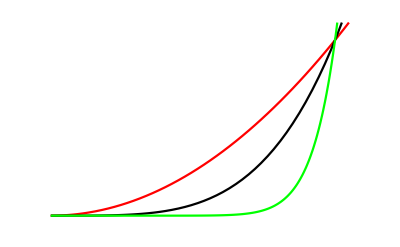

```mathematica
f[n_,x_]:=x^n;
textStyle={FontFamily->"LM Roman 12",FontSize->30};
pl1:=Plot[Evaluate[Table[f[n,x],{n,{2,4,12}}]],{x,0,1.1},PlotRange->{{-0.05, 1.1},{-0.05,1.1}}, PlotStyle->{ {Red,Thick},  {Black,Thick}, {Green,Thick}},   (*PlotLegends->SwatchLegend[MaTeX[Table[f[n,x],{n,4,16,4}],Magnification->2]], *)  
PlotLegends->SwatchLegend[MaTeX[{"f_2(x)=x^2","f_4(x)=x^4", "f_{16}(x)=x^{16}" },Magnification->2]],
BaseStyle->textStyle, Axes->False,TicksStyle-> Directive[Black,20],
AxesStyle->{{Thick,Black},{Thick,Black}},
LabelStyle->Directive[FontSize->30,FontFamily->"LM Roman 12"]];pl1(*Filling->Axis*)
```

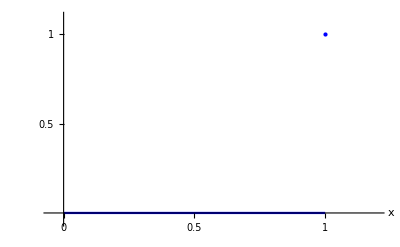

```mathematica
textStyle={FontFamily->"LM Roman 12",FontSize->30};
pl2:=Plot[{0},{x,0,1},PlotRange->{{-0.05, 1.2},{-0.05,1.1}}, BaseStyle->textStyle,TicksStyle-> Directive[Black,20],AxesLabel->Automatic, AxesStyle->{{Thick,Black},{Thick,Black}}, 
PlotStyle->  {Blue,Thickness-> 0.015},Ticks->{{0,.5,1},{.5,1}},
Ticks-> False, PlotLegends->SwatchLegend[MaTeX[{"f(x)"},Magnification->2]],
Epilog->{Blue,PointSize@Large,Point[{1,1}]}];
pl2
```

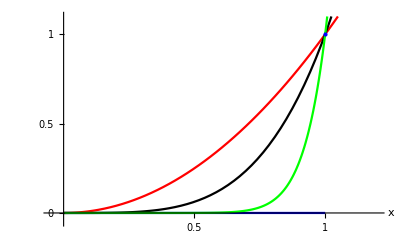

```mathematica
pl3:=Show[pl2, pl1, Ticks->{{0.5,1},{ 0,.5,1}}];
pl3
```

```mathematica
Export["7-1.pdf",pl3]
```

7-1.pdf

```mathematica
pl4:=Plot[{1/2},{x,0,1},PlotRange->{{0, 1.1},{0,1.1}}, BaseStyle->textStyle,Ticks->False,TicksStyle-> Directive[Black,20],PlotStyle->  {Blue,Dashed,Thickness-> 0.005}]
```

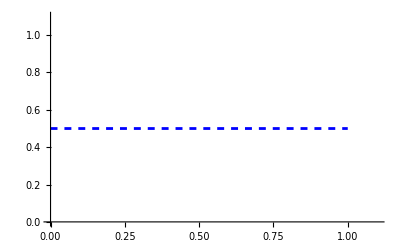

```mathematica
pl4
```

```mathematica
pl5:=Show[pl3,pl4,Epilog->{Blue,PointSize@Large,Point[{1,1}],Inset[MaTeX["\\varepsilon=0.5",Magnification->2],{0.4, 0.7},Scaled[{0.5,1}]]}]
```

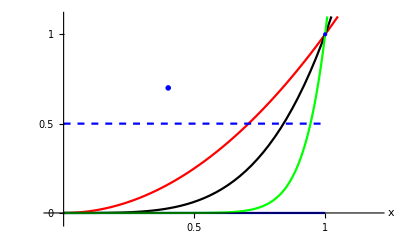

```mathematica
pl5
```

```mathematica
Export["7-5.pdf",pl5]
```

7-5.pdf

## Figure 7.2

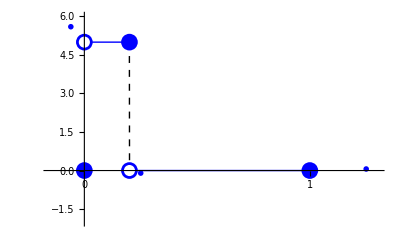

```mathematica
extStyle={FontFamily->"LM Roman 12",FontSize->20};
f3[x_]:=Piecewise[{{5,0<x<1/5}, {0,1/5≤ x≤ 1}}];
epilog={PointSize[0.03],Blue,Point[{0,0}],
	PointSize[0.03],Blue,Point[{0.2,0}],
              PointSize[0.02],White,Point[{0.2,0}],
              PointSize[0.03],Blue,Point[{0.2,5}],
              PointSize[0.03],Blue,Point[{5,0}],
PointSize[0.03],Blue,Point[{0,5}],
PointSize[0.02],White,Point[{0,5}],
 PointSize[0.03],Blue,Point[{1,0}],
Inset[MaTeX["x",Magnification->2],{1.25, 0.06},Scaled[{0.5,1}]],
Inset[MaTeX["n",Magnification->2],{-0.06,5.6},Scaled[{0.5,1}]],
Inset[MaTeX["\\frac1n",Magnification->1.7],{0.25,-0.1},Scaled[{0.5,1}]]};
plotf:=Plot[f3[x],{x,0,1},PlotRange->{{-0.15, 1.3},{-2, 6}},BaseStyle->textStyle,Ticks-> {{0, 1},False},TicksStyle-> Directive[Black,20],PlotStyle->{{Blue,Thick},{Red,Thick},  {Orange,Thick}},  ExclusionsStyle->{{Black,Dashed},Blue}, Epilog-> epilog]
plotf
```

```mathematica
Export["7-2.pdf",plotf]
```

7-2.pdf

## Figure 7.3

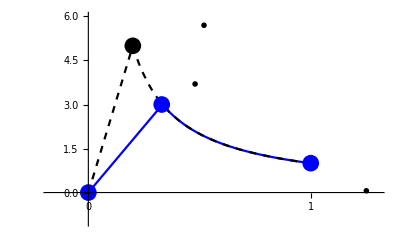

```mathematica
extStyle={FontFamily->"LM Roman 12",FontSize->20};
f3[x_]:=Piecewise[{{9x,0<=x<1/3}, {1/x,1/3≤ x≤ 1}}];
f4[x_]:=Piecewise[{{25x,0<=x<1/5}, {1/x,1/5≤ x≤ 1}}];
epilog={PointSize[0.03],Blue,Point[{0.33,3}],
              PointSize[0.03],Blue,Point[{5,0}],
PointSize[0.03],Blue,Point[{0,0}],
 PointSize[0.03],Blue,Point[{1,1}],
PointSize[0.03],Black,Point[{0.2,5}],
Inset[MaTeX["x",Magnification->2],{1.25, 0.06},Scaled[{0.5,1}]],
Inset[MaTeX["(1/n , n)",Magnification->1.6],{0.48,3.7},Scaled[{0.5,1}]],
Inset[MaTeX["(1/(n+1) , n+1)",Magnification->1.6],{.52,5.7},Scaled[{0.5,1}]]};
ploth:=Plot[{f3[x],f4[x]},{x,0,1},PlotRange->{{-0.17, 1.3},{-1, 6}},BaseStyle->textStyle,TicksStyle-> Directive[Black,20],Ticks-> {{0, 1},False},PlotStyle->{{Blue,Thick},{Black,Thick,Dashed},  {Orange,Thick}},  ExclusionsStyle->{{Black,Dashed},Blue}, Epilog-> epilog, PlotLegends->SwatchLegend[MaTeX[{"h_n", "h_{n+1}"},Magnification->1.8]]];
ploth
```

```mathematica
Export["7-3.pdf",ploth]
```

7-3.pdf

## Figure 7.4

```mathematica
h[n_,x_]:=1+x+Sin[x]+4Sin[1+n*x]/n
textStyle={FontFamily->"LM Roman 12",FontSize->20};
plot1:=Plot[{Evaluate[Table[h[n, x], {n, {2,5, 8}}]]},{x,0,5},PlotRange->{{-0.1, 4},{-0.2, 7}},PlotStyle->{{Gray,Thick},{Red,Thick},  {Orange,Thick}},    BaseStyle->textStyle, Axes->False,  TicksStyle-> Directive[Black,20], 
(*PlotLegends->SwatchLegend[MaTeX[{"f_{N-1}(x)","f_N(x)"},Magnification->2]], PlotLegends->"Expressions",*) Epilog->{Arrow[{{1,5},{1.3,4}}],Inset[MaTeX["f_N",Magnification->2],{1,6},Scaled[{0.5,1}]], 
Arrow[{{2.5,1.5},{2,2}}],Inset[MaTeX["f_{N-1}",Magnification->2],{2.6,2.5},Scaled[{0.5,1}]]}]
```

```mathematica
plot2:=Plot[{1+x+Sin[x], 2+x+Sin[x], x+Sin[x]},{x,0,5},PlotRange->{{-0.1, 4},{-0.2, 7}},    BaseStyle->textStyle,Axes->False,  TicksStyle-> Directive[Black,20],PlotStyle->{{Black,Thick},  {Blue,Thick},  {Blue,Thick}},(*PlotLegends->SwatchLegend[MaTeX[{"f(x)","f(x)+\epsilon", "f(x)-\epsilon"},Magnification->2]],PlotLegends->"Expressions",*)
Epilog->{Arrow[{{1,5},{1.2,4.2}}],Inset[MaTeX["f + \\varepsilon",Magnification->2],{0.9,5.8},Scaled[{0.5,1}]], 
Arrow[{{1.4,1.25},{1.2,2.1}}],Inset[MaTeX["f - \\varepsilon",Magnification->2],{1.4,1.4},Scaled[{0.5,1}]],
Arrow[{{3.8,2.2},{3.2,4.1}}],Inset[MaTeX["f",Magnification->2],{3.9,2.7},Scaled[{0.5,1}]],
Arrow[{{2.2,5.8},{2.5,4.8}}],Inset[MaTeX["f_N",Magnification->2],{2.2,7},Scaled[{0.5,1}]],
Arrow[{{2.35,2.2},{2.75,3.7}}],Inset[MaTeX["f_n\; (n\\ge  N)",Magnification->2],{2.8,2.5},Scaled[{0.5,1}]]}]
```

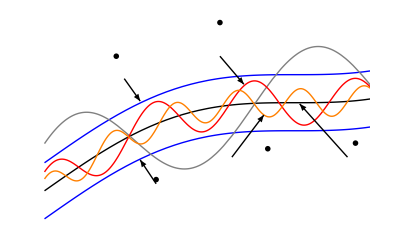

```mathematica
plotu:=Show[plot2, plot1];
plotu
```

```mathematica
Export["7-4.pdf",plotu]
```

7-4.pdf

## Template

```mathematica
(*SystemOpen[DirectoryName[AbsoluteFileName["7-2.pdf"]]]*)
```

```mathematica
(*SystemOpen["7-2.pdf"]*)
```

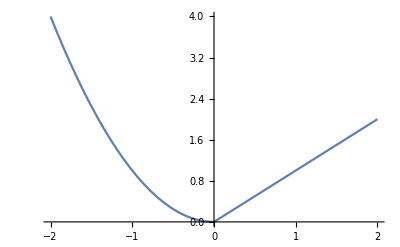

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
```

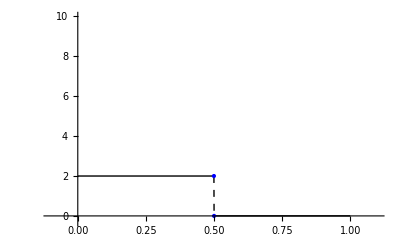

```mathematica
extStyle={FontFamily->"LM Roman 12",FontSize->20};
f2[x_]:=Piecewise[{{0,1/2<=x<=1}, {2,0<x<1/2}}];
epilog={};
p1:=Plot[f2[x],{x,0,1},PlotRange->{{-0.1, 1.1},{-0.3, 10}},BaseStyle->textStyle,PlotStyle->{{Black,Thick},{Red,Thick},  {Orange,Thick}}, ExclusionsStyle->{{Black,Dashed},Blue}, Epilog-> epilog, TicksStyle-> Directive[Black,20]];
p1
```

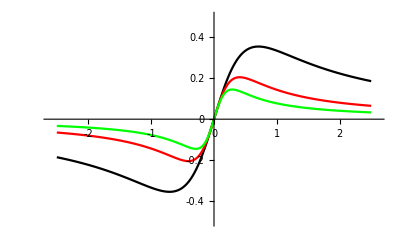

```mathematica
f9[n_, x_]:= x/(1+n*x^2);
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{lmodern}"}];
textStyle={FontFamily->"LM Roman 12",FontSize->20};
plot0:=Plot[Evaluate[Table[f9[n,x],{n,{2,6,12}}]],{x,-2.5,2.5},PlotRange->{{-2.6, 2.6},{-0.5,0.5}}, PlotStyle->{ {Black,Thick},  {Red,Thick}, {Green,Thick}},
PlotLegends->SwatchLegend[MaTeX[{"f_2(x)","f_6(x)", "f_{12}(x)"},Magnification->1.5]],PlotLegends->"Expressions",    
BaseStyle->textStyle, TicksStyle-> Directive[Black,16],Ticks->{{-2, -1, 0,1, 2}, {-0.4, -0.2, 0,0.2, 0.4}}];
plot0(*Filling->Axis*)
```

```mathematica
Export["7-6.pdf",plot0]
```

7-6.pdf